# 分形

二维科赫曲线

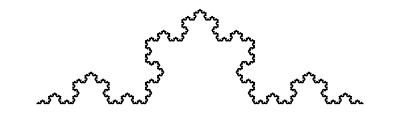

```mathematica
Graphics[KochCurve[5]]
```

科赫雪花的前4个迭代

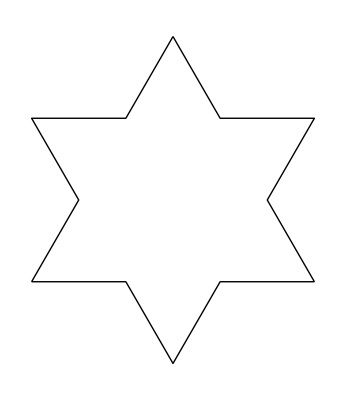
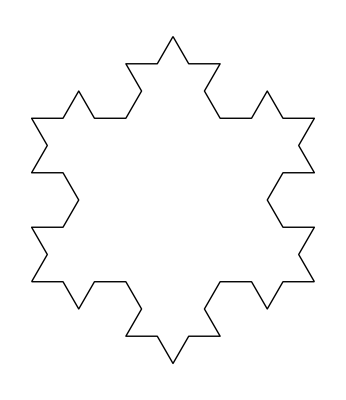
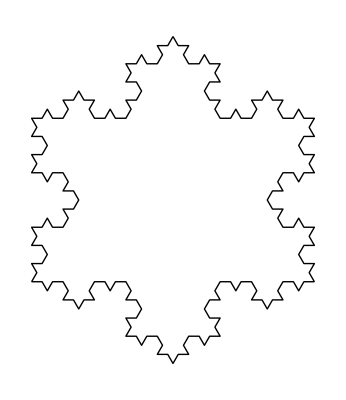
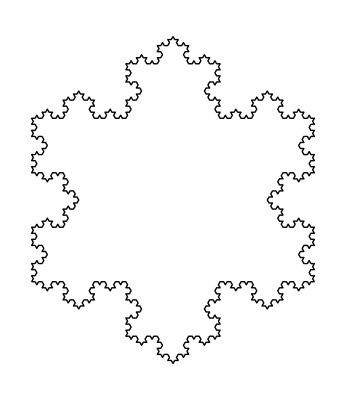

```mathematica
Table[Graphics[GeometricTransformation[KochCurve[i],{RotationTransform[π/3,{0,0}],RotationTransform[-π/3,{1,0}],RotationTransform[π,{1/2,0}]}]],{i,4}]//Row
```

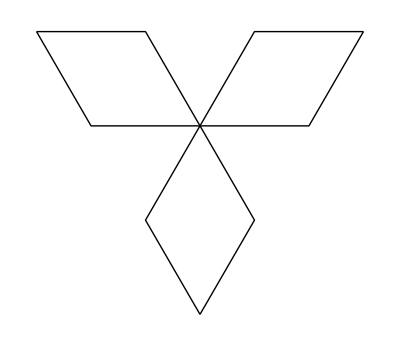
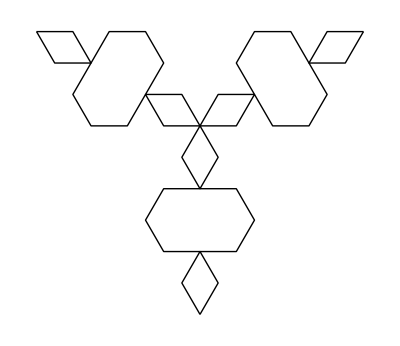
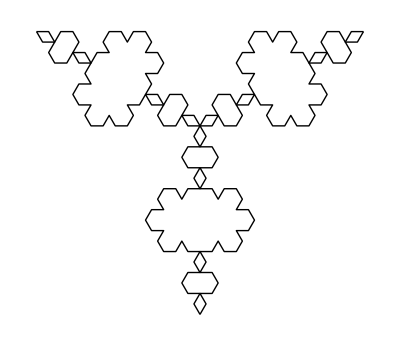
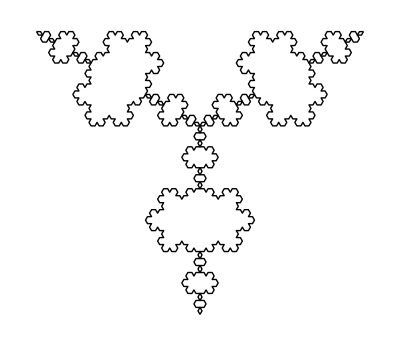

```mathematica
Table[Graphics[GeometricTransformation[KochCurve[i],{RotationTransform[π/3,{1,0}],RotationTransform[-π/3,{0,0}],RotationTransform[π,{1/2,0}]}]],{i,4}]//Row
```

二维希尔伯特曲线：

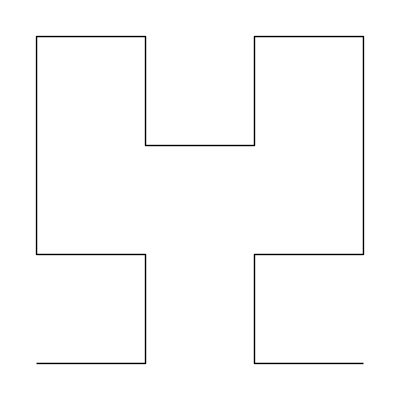

```mathematica
Graphics[HilbertCurve[2]]
```

用样条线可视化二维希尔伯特曲线：

```mathematica
Graphics[{Thickness[Large],HilbertCurve[4]/.Line->BSplineCurve}]
```

-Graphics-

二维皮亚诺曲线：

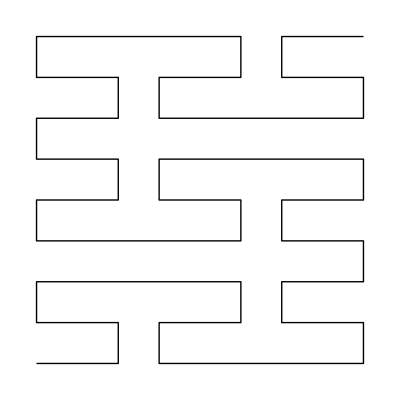

```mathematica
Graphics[PeanoCurve[2]]
```

可视化带有样条曲线的二维皮亚诺曲线：

```mathematica
Graphics[{Thickness[Large],PeanoCurve[3]/.Line->BSplineCurve}]
```

-Graphics-

二维谢尔宾斯基曲线：

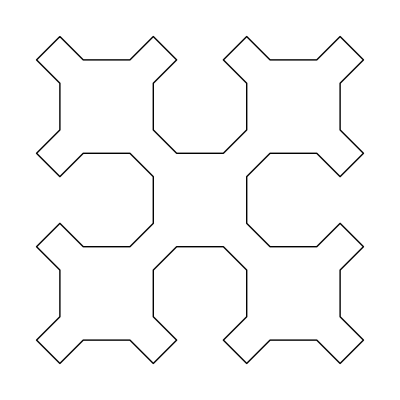

```mathematica
Graphics[SierpinskiCurve[2]]
```

用样条线可视化二维谢尔宾斯基曲线：

```mathematica
Graphics[{Thickness[Large],SierpinskiCurve[3]/.Line->BSplineCurve}]
```

-Graphics-